# The Walking Dead : Malaria Edition

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
(*Markov*)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

LakeMatrixPlot

LakeNetwork

## Inputs

Style

```mathematica
edgeChopThreshold=10^-2;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
```

Geo - Setting

```mathematica
{citiesNumber,networkDimension,distance}={6,3,2};
(**)
movementProbabilitiesVector=ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&;
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)

## Spatial Setting

2 D - Grid

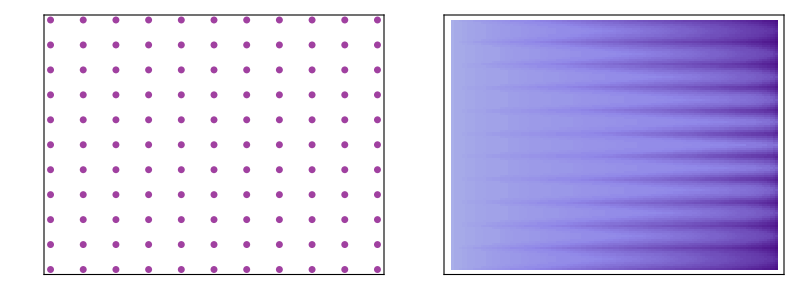

```mathematica
citiesSqrt=distance*Sqrt[citiesNumber]//Round;
sampledCoordinates=Tuples[Range[-citiesSqrt,citiesSqrt],2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
(**)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}]
```

Movement Kernel

### Inverse-Linear Kernel

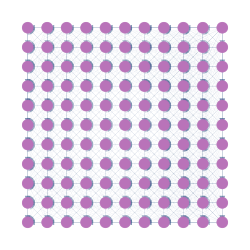

```mathematica
migrationProbabilities=CalculateInverseLinearKernelMigrationProbabilities[euclideanDistances,0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
originalMap = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migrationProbabilities,{i_,i_}->0]//LowerTriangularize,edgeChopThreshold],
ToString /@ Range[Length[migrationProbabilities]]
   }, .1
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->250
,LineThickness->.0025
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexStyle->stylesListType
,VertexLabelStyle->.001
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
  ]
```

### Exponential Kernel

Markov Baseline

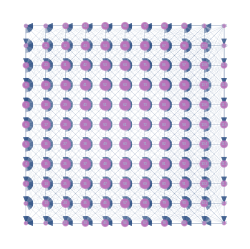

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline= GraphTransitionsFrequenciesWithMax[
  {
Chop[migrationProbabilities//LowerTriangularize,edgeChopThreshold],
ToString /@ Range[Length[migrationProbabilities]]
   }, .05
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->250
,LineThickness->.0005
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]]
,VertexStyle->stylesListType
,VertexLabelStyle->.001
  ]
```

## Network Dimensionality

Dimensions

{2,1,3,3,1,3,1,3,2,2,2,3,2,2,1,3,1,1,3,1,2,3,1,1,3,2,3,2,3,3,3,2,3,2,2,2,2,1,3,1,2,2,3,1,3,2,1,1,3,1,3,1,2,3,2,2,2,2,3,2,2,2,2,3,3,1,3,2,2,2,1,3,1,3,1,2,3,3,3,2,1,2,1,1,1,3,2,1,3,3,3,2,2,3,2,2,1,3,1,3,2,2,1,1,3,1,3,2,2,2,3,1,3,3,1,2,1,2,3,2,1}

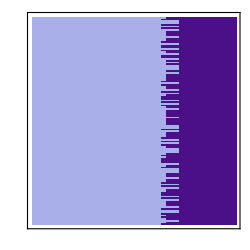

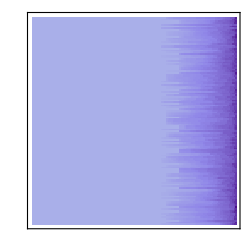

```mathematica
cityType=RandomChoice[Range[networkDimension],sampledCoordinates//Length]
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"]
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"]
```

Markov Dimensional Network

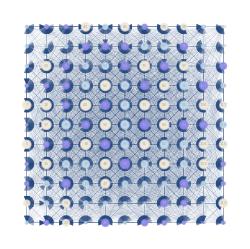

```mathematica
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.001,.9}}],Arrow[e]}
markovDimensional= GraphTransitionsFrequenciesWithMax[
  {
Chop[migrationDimensionalMatrix,edgeChopThreshold],
ToString /@ Range[Length[migrationDimensionalMatrix]]
   }, .1
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->250
,LineThickness->.0005
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[markovPDF]]]
,VertexStyle->stylesListType
,VertexLabelStyle->.001
  ]
```

## Attractors/Repellents

Attractors

Repellents

## Report

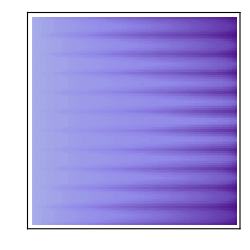
Original Grid | Dimensions Mask | Applied Mask
-Graphics- | -Graphics- | -Graphics-
 |  | 
Distances Matrix | Dimensions Matrix | Applied Dimensions
-Graphics- | -Graphics- | -Graphics-
 |  |

```mathematica
Grid[{
{"Original Grid","Dimensions Mask","Applied Mask"},
{originalMap,markovBaseline,markovDimensional},
{"","",""},
{"Distances Matrix","Dimensions Matrix","Applied Dimensions"},
{matrixDistancesPlot,matrixPenalizationsPlot,matrixDimensionalPlot},
{"","",""}
}]
```